# A naive model for the vertical motion of an air bubble in water

Alessandro Gentilini (5th January 2021)

## Introduction

I attended courses in free and SCUBA diving and they explained us the basic gas laws, during a lesson I was asking myself: what is the motion of an air bubble generated as some depth in the sea?

## A naive model

The motion equation in one dimension is
 m(ⅆ^2 y)/(ⅆ t^2)=F  
 where t is time, y is the depth in the water and F sums all the relevant forces applied to the bubble. y=0 is the water level and y<0 is below the water.
F is the sum of just two component: 
F=-m g + A  
where m is the mass of the bubble, g is the gravity acceleration and A is the Archimede’s force. The Archimede’s force is the product of the density ρ of the water, the volume V of the bubble and the the gravity acceleration: A=ρ V g.
But the volume of the air bubble depends on the pressure p according to the perfect gas law: p V = n R T where n is the number of moles of air, R is the gas constant and T is the temperature.
The pressure p at depth y is due to the water column (so called hydrostatic pressure): p=-ρ g y.
The number of moles n is related to the molar mass of the air M and the bubble mass m through n=m/M.
So
 V=(n R T)/p=m/M·(R T)/(-ρ g y) 
 and
 F=-m g + ρ V g
 Substituting V in F I get
 F=-m g + ρ g·m/M·(R T)/(-ρ g y)  
 and I can simplify ρ g (so this model is valid for any fluid? Uhmmm... first doubt about my naive model) to get
  F=-m g -m/M·(R T)/y  
 Now the sum of forces must be balanced by the product of the mass of the bubble and its acceleration:
  m(ⅆ^2 y)/(ⅆ t^2)=-m g -m/M·(R T)/y    
 I can simplify the mass of the bubble (uhm... second doubt about this model):
    (ⅆ^2 y)/(ⅆ t^2)=- g -(R T)/M·1/y    
 So let’s try to solve it symbolically!

## Solution of the differential equation

```mathematica
DSolve[y''[t]==-g-(R*T)/(M*y[t]),y[t],t]
```

Solve[(1/(√(C[1]+2 (-g K[1]-(R T Log[K[1]])/M)))K[1]1y[t])^2==(t+C[2])^2,y[t]]

OK, it seems it cannot be solved... so I look for a numerical solution; first of all I set some values (in SI units):

```mathematica
R:=8.31
T:=293
M:=28.97/1000
g:=9.8
h:=-10
```

And then solve it numerically:

```mathematica
ysol=NDSolveValue[{y''[t]==-g-(R*T)/(M*y[t]),y[0]==h,y'[0]==0},y,{t,0,10}]
```

NDSolveValue::ndsz: At t == 0.0432523, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction[…]

I would say the problem is the singularity (even because I do not know what a stiff system is ☺).
This is the plot of  the depth y vs time t:

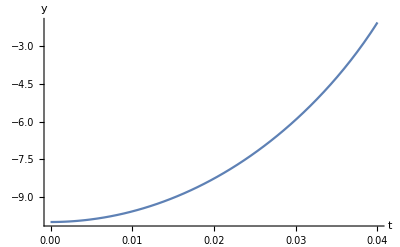

```mathematica
Plot[ysol[t],{t,0,0.04},AxesLabel->{t,y}]
```

And this is the plot of the bubble radius multiplied by a constant k:

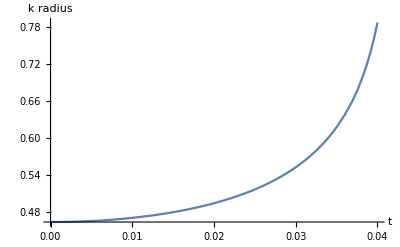

```mathematica
kradius[t_]:=CubeRoot[-1/ysol[t]]
Plot[kradius[t],{t,0,0.04},AxesLabel->{t,k radius}]
```

Now I would like to draw the bubble in ten equispaced time instants (copied from https://mathematica.stackexchange.com/a/207586 )

```mathematica
bubble[t_]:=Circle[{0,ysol[t]},kradius[t]]
```

```mathematica
Graphics[{bubble /@ Array[#&,10,{0,0.04}]},ImageSize->50]
```

-Graphics-

## An animation

An animation (copied from https://mathematica.stackexchange.com/a/17205 ):

```mathematica
Manipulate[Graphics[{Circle[{0,ysol[t]},kradius[t]]},PlotRange->{{-1,1},{-11,0}}],{t,0,0.04}]
```

## What’s wrong with this model?

The main problem I can see, based on my limited experience in observing bubbles, is that it neglects the “friction” of the water acting on the moving bubble: I remember that I saw bubbles starting as sphere but then deforming into mushroom-like shapes.
Then I have doubts about the mass of my bubble.

I think this model will make physicists laughing (and numerical analysts too)... but I am not able to grasp the 1917 formulation by Lord Rayleigh and my Mathematica trial license is soon expiring! If I had had more time I would have tried to solve the Lord Rayleigh’s equation.

## Further readings

Lord Rayleigh O.M. F.R.S. (1917) VIII. On the pressure developed in a liquid during the collapse of a spherical cavity, The London, Edinburgh, and Dublin Philosophical Magazine and Journal of Science, 34:200, 94-98, DOI: 10.1080/14786440808635681